```mathematica
pivot[iStar_, jStar_, tableau_] := (
newTableau = tableau;
numberRows = Dimensions[tableau][[1]];
numberCols = Dimensions[tableau][[2]];
(* switch row tableau variables *)
newTableau[[1,jStar]] = tableau[[iStar, numberCols]];
newTableau[[iStar, numberCols]] = tableau[[1,jStar]];
(* switch column tableau variables *)
newTableau[[numberRows,jStar]] = -tableau[[iStar, 1]];
newTableau[[iStar, 1]] = -tableau[[numberRows,jStar]];
(* adjust loop bounds to skip 1st column and last row *)
For[ii = 2, ii < numberRows, ii++,
For[jj=2,jj<numberCols,jj++,
If[ii == iStar && jj == jStar, 
newTableau[[ii,jj]]=1/tableau[[iStar, jStar]]];
If[ii== iStar && jj ≠ jStar,
newTableau[[ii,jj]]= -tableau[[iStar, jj]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj == jStar,
newTableau[[ii, jj]]= tableau[[ii, jStar]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj ≠ jStar,
newTableau[[ii,jj]] = tableau[[ii,jj]]-tableau[[iStar,jj]]*tableau[[ii, jStar]]/tableau[[iStar,jStar]]];
]
];
Return[newTableau];
)
```

```mathematica
Clear[x1,x2]
z[x1_,x2_]=17x1+11x2-9; delz={17,11};
g1[x1_,x2_]:=2x1+x2; b1=32;delg1={2,1};
g2[x1_,x2_]:=x1+x2; b2=20;delg2={1,1};
g3[x1_,x2_]:=1x1+2x2;b3=38;delg3={1,2}; 


g1[x1_]:=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
g2[x1_]:=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]]
g3[x1_]:=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]]
```

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-1,40},AspectRatio->Automatic,PlotRange->{-1,40},PlotHighlighting->None ]
```

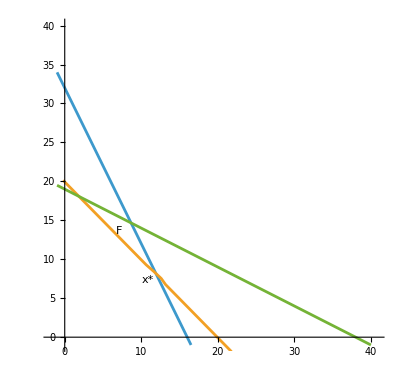

```mathematica
db1=0;
db2=0;
db3=0;
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,1,1,-17,"v1"};
m2={"x2",1,1,2,-11,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-9,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
```

db = ( 0 0 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 1 | 1 | -17 | v1
x2 | 1 | 1 | 2 | -11 | v2
-1 | 32 | 20 | 38 | -9 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

```mathematica
b = pivot[2,2, a]
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[b]];
```

{{ ,v1,y2,y3,1, },{s1,1/2,-1/2,-1/2,17/2,y1},{x2,1/2,1/2,3/2,-5/2,v2},{-1,16,4,22,263,w→min},{,-x1,-s2,-s3,-z→min,}}

db = ( 0 0 0 ) initial = (  | v1 | y2 | y3 | 1 |  
s1 | 1/2 | -1/2 | -1/2 | 17/2 | y1
x2 | 1/2 | 1/2 | 3/2 | -5/2 | v2
-1 | 16 | 4 | 22 | 263 | w→min
 | -x1 | -s2 | -s3 | -z→min | )

```mathematica
c = pivot[2,3, b]
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[c]];
```

{{ ,v1,y1,y3,1, },{s2,1,-2,-1,17,y2},{x2,1,-1,1,6,v2},{-1,20,-8,18,331,w→min},{,-x1,-s1,-s3,-z→min,}}

db = ( 0 0 0 ) initial = (  | v1 | y1 | y3 | 1 |  
s2 | 1 | -2 | -1 | 17 | y2
x2 | 1 | -1 | 1 | 6 | v2
-1 | 20 | -8 | 18 | 331 | w→min
 | -x1 | -s1 | -s3 | -z→min | )

```mathematica
d = pivot[3,3,c]
Print["db = ( ",db1," ",db2," ",db3," ) opt = ",MatrixForm[d]];
```

{{ ,v1,v2,y3,1, },{s2,-1,2,-3,5,y2},{s1,1,-1,1,6,y1},{-1,12,8,10,283,w→min},{,-x1,-x2,-s3,-z→min,}}

db = ( 0 0 0 ) opt = (  | v1 | v2 | y3 | 1 |  
s2 | -1 | 2 | -3 | 5 | y2
s1 | 1 | -1 | 1 | 6 | y1
-1 | 12 | 8 | 10 | 283 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
xStar1Base = 12; xStar2Baser = 8; 
zStar = 283; 
xStarBase={x1StarBase,x2StarBase}
yStar1Base = 6; yStar2Base = 5; yStar3Base = 0
wStar = 283; 
yStar = {yStar1Base, yStar2Base, yStar3Base}
```

{x1StarBase,x2StarBase}

{x1StarBase,x2StarBase}

0

{6,5,0}

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-1,40},AspectRatio->Automatic,PlotRange->{-1,40},PlotHighlighting->None ]
```

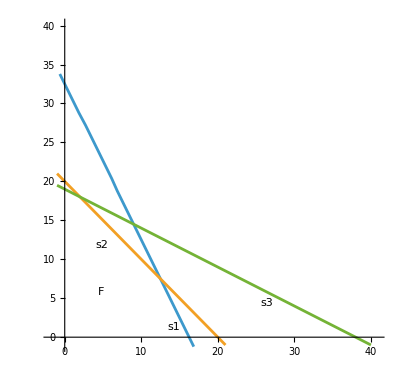

```mathematica
(*db1 max and min*)
Plot[{g1[x],g2[x],g3[x]},{x,-1,40},AspectRatio->Automatic,PlotRange->{-1,40},PlotHighlighting->None ]
```

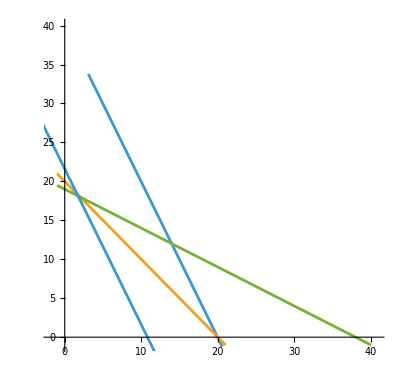

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-1,40},AspectRatio->Automatic,PlotRange->{-1,40},PlotHighlighting->None ]
```

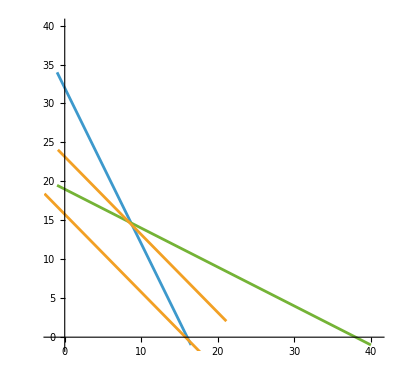

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-1,40},AspectRatio->Automatic,PlotRange->{-1,40},PlotHighlighting->None ]
(*no db3 max, b3 is not included in the xstar solution*)
```

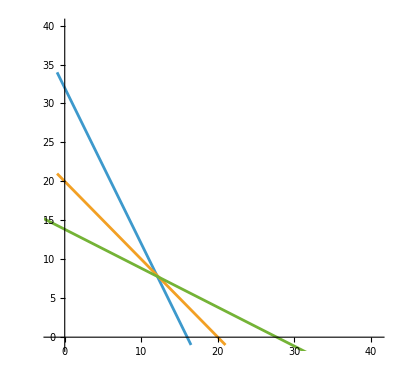

```mathematica
Solve[g2[u,v]==b2&&g3[u,v]==b3]
b1Min = g1[2,18]
db1Min = b1Min - b1
```

{{u→2,v→18}}

22

-10

```mathematica
Solve[g1[u,v]==b1&&g3[u,v]==b3]
```

{{u→26/3,v→44/3}}

```mathematica
b2Max = g2[26/3, 44/3]
db2Max = b2Max - b2
```

70/3

10/3

```mathematica
Solve[g1[u,v]==b1&&v==0]
```

{{u→16,v→0}}

```mathematica
b2Min = g2[16,0]
db2Min = b2 - b2Min
```

16

4

```mathematica
Solve[g1[u,v]==b1&&g2[u,v]==b2]
```

{{u→12,v→8}}

```mathematica
b3min=g3[12,8]
db3min=b3min-b3
```

28

-10

```mathematica
(*Part 4*)
(*a*)
db1=0;
db2=2;
db3=0;
(* resCost=p1 (b1+db1)+p2 (b2+db2)+p3 (b3+db3) *)
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,1,1,-17,"v1"};
m2={"x2",1,1,2,-11,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-9,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
```

db = ( 0 2 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 1 | 1 | -17 | v1
x2 | 1 | 1 | 2 | -11 | v2
-1 | 32 | 22 | 38 | -9 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

```mathematica
b = pivot[2,2, a]
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[b]];
```

{{ ,v1,y2,y3,1, },{s1,1/2,-1/2,-1/2,17/2,y1},{x2,1/2,1/2,3/2,-5/2,v2},{-1,16,6,22,263,w→min},{,-x1,-s2,-s3,-z→min,}}

db = ( 0 2 0 ) initial = (  | v1 | y2 | y3 | 1 |  
s1 | 1/2 | -1/2 | -1/2 | 17/2 | y1
x2 | 1/2 | 1/2 | 3/2 | -5/2 | v2
-1 | 16 | 6 | 22 | 263 | w→min
 | -x1 | -s2 | -s3 | -z→min | )

```mathematica
c = pivot[2,3, b]
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[c]];
```

{{ ,v1,y1,y3,1, },{s2,1,-2,-1,17,y2},{x2,1,-1,1,6,v2},{-1,22,-12,16,365,w→min},{,-x1,-s1,-s3,-z→min,}}

db = ( 0 2 0 ) initial = (  | v1 | y1 | y3 | 1 |  
s2 | 1 | -2 | -1 | 17 | y2
x2 | 1 | -1 | 1 | 6 | v2
-1 | 22 | -12 | 16 | 365 | w→min
 | -x1 | -s1 | -s3 | -z→min | )

```mathematica
d = pivot[3,3, c]
Print["db = ( ",db1," ",db2," ",db3," ) opt = ",MatrixForm[d]];
```

{{ ,v1,v2,y3,1, },{s2,-1,2,-3,5,y2},{s1,1,-1,1,6,y1},{-1,10,12,4,293,w→min},{,-x1,-x2,-s3,-z→min,}}

db = ( 0 2 0 ) opt = (  | v1 | v2 | y3 | 1 |  
s2 | -1 | 2 | -3 | 5 | y2
s1 | 1 | -1 | 1 | 6 | y1
-1 | 10 | 12 | 4 | 293 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
delZ = {17,11};
delg1 = {2,1}; delg2 = {1,1}; delg3={1,2};
dzStar = 293 - zStar;
xStarNew = {10,12};
dxStar = xStarNew - xStarBase;
Print[dzStar == delZ.dxStar == (yStar1Base delg1 + yStar2Base delg2 + yStar3Base delg3).dxStar == yStar1Base db1 + yStar2Base db2 + yStar3Base db3]
```

10==17 (10-x1StarBase)+11 (12-x2StarBase)==17 (10-x1StarBase)+11 (12-x2StarBase)==10